# q q^-→ g g (With Ghosts)

## Feynman diagrams (s, t, u)

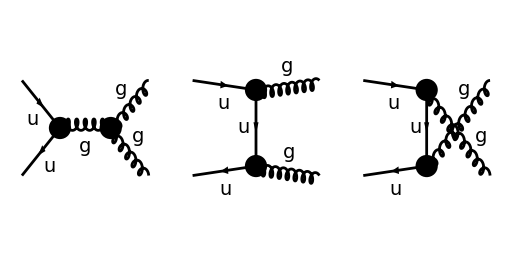

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagsG = InsertFields[T1, {F[3, {1}], -F[3, {1}]} ->
		{V{5},V{5}}, InsertionLevel -> {Classes},
		Model -> "SMQCD", ExcludeParticles -> {S[1], S[2], V[1],V[2],V[3]}];
Paint[diagsG, ColumnsXRows -> {3, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

## Ghosts

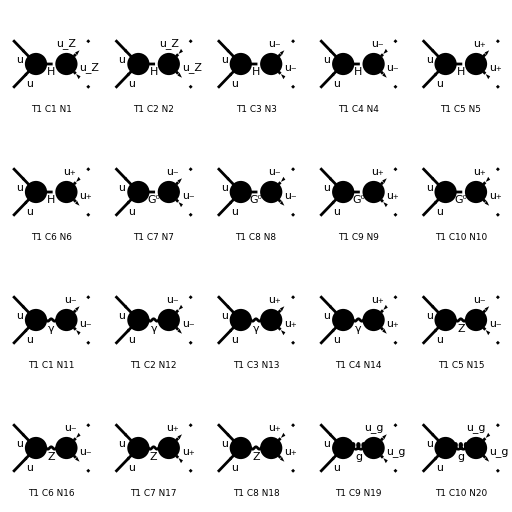

```mathematica
W=CreateTopologies[0, 2 -> 2];
diagW = InsertFields[W, {F[3, {1}], -F[3, {1}]} ->{ U{5} , U{5} }, InsertionLevel -> {Classes},GenericModel -> "Lorentz",Model -> "SMQCD"];
Paint[diagW,ColumnsXRows -> {5, 5},ImageSize->{512,512}];
```

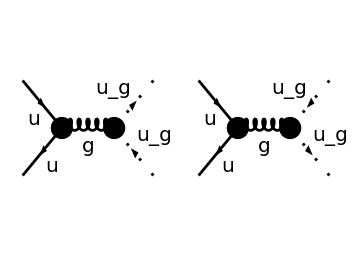

```mathematica
Ghosts = InsertFields[W, {F[3, {1}], -F[3, {1}]} ->{ U{5} , U{5} }, InsertionLevel -> {Classes},GenericModel -> "Lorentz",Model -> "SMQCD",ExcludeParticles -> {S[1], S[2], V[1],V[2],V[3]}];
Paint[Ghosts,ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{352,256}];
```

## All Contributing Diagrams

-Graphics-

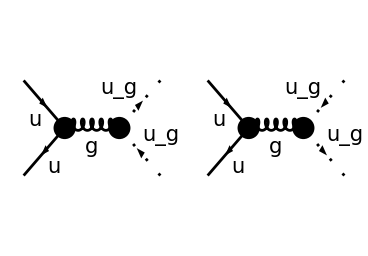

```mathematica
T1All=CreateTopologies[0, 2 -> 2];
diagsG = InsertFields[T1, {F[3, {1}], -F[3, {1}]} ->
		{V{5},V{5}}, InsertionLevel -> {Classes},
		Model -> "SMQCD", ExcludeParticles -> {S[1], S[2], V[1],V[2],V[3]}];
Paint[diagsG, ColumnsXRows -> {3, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
Ghosts = InsertFields[W, {F[3, {1}], -F[3, {1}]} ->{ U{5} , U{5} }, InsertionLevel -> {Classes},GenericModel -> "Lorentz",Model -> "SMQCD",ExcludeParticles -> {S[1], S[2], V[1],V[2],V[3]}];
Paint[Ghosts,ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{368,256}];
```

## Amplitude (M_1,M_2,M_3)

```mathematica
QQbar =(FCFAConvert[CreateFeynAmp[diagsG,Truncated -> False],IncomingMomenta->{Subscript[p, 1],Subscript[p, 2]},OutgoingMomenta->{Subscript[k, 1],Subscript[k, 2]},
DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True,List->False,TransversePolarizationVectors->{Subscript[k, 1],Subscript[k, 2]},SMP->True])
```

((ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col5^Glu3).(γ·(k_1-p_2)+m_u).(-ⅈ g_s γ^Lor2 T_Col5Col1^Glu4).(φ(p_1,m_u)))/((p_2-k_1)^2-m_u^2)+((ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor2 T_Col2Col5^Glu4).(γ·(k_2-p_2)+m_u).(-ⅈ g_s γ^Lor1 T_Col5Col1^Glu3).(φ(p_1,m_u)))/((p_2-k_2)^2-m_u^2)-(g_s g^Lor3Lor4 (ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) f^Glu3Glu4Glu5 ((k_1+2 k_2)^Lor1 g^Lor2Lor4+(-2 k_1-k_2)^Lor2 g^Lor1Lor4+(k_1-k_2)^Lor4 g^Lor1Lor2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor3 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2

## Amplitude (M_G1,M_G2)

```mathematica
QQbarGhosts =(FCFAConvert[CreateFeynAmp[Ghosts,Truncated -> False],IncomingMomenta->{Subscript[p, 1],Subscript[p, 2]},OutgoingMomenta->{Subscript[k, 1],Subscript[k, 2]},
DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True,List->False,TransversePolarizationVectors->{Subscript[k, 1],Subscript[k, 2]},SMP->True])
```

(g_s k_2^Lor2 g^Lor1Lor2 f^Glu3Glu4Glu5 (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2-(g_s k_1^Lor2 g^Lor1Lor2 f^Glu3Glu4Glu5 (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2

## Total Amplitude FeynCalc

```mathematica
QQbar+QQbarGhosts
```

((ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col5^Glu3).(γ·(k_1-p_2)+m_u).(-ⅈ g_s γ^Lor2 T_Col5Col1^Glu4).(φ(p_1,m_u)))/((p_2-k_1)^2-m_u^2)+((ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor2 T_Col2Col5^Glu4).(γ·(k_2-p_2)+m_u).(-ⅈ g_s γ^Lor1 T_Col5Col1^Glu3).(φ(p_1,m_u)))/((p_2-k_2)^2-m_u^2)-(g_s g^Lor3Lor4 (ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) f^Glu3Glu4Glu5 ((k_1+2 k_2)^Lor1 g^Lor2Lor4+(-2 k_1-k_2)^Lor2 g^Lor1Lor4+(k_1-k_2)^Lor4 g^Lor1Lor2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor3 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2-(g_s k_1^Lor2 g^Lor1Lor2 f^Glu3Glu4Glu5 (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2+(g_s k_2^Lor2 g^Lor1Lor2 f^Glu3Glu4Glu5 (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2

## Simplified Denominators

```mathematica
GAD[μ](GSD[Subscript[k, 1]-Subscript[p, 2]]+ m).GAD[ν]*FeynAmpDenominator[PropagatorDenominator[Subscript[k, 1]-Subscript[p, 2],Subscript[m, q]]]//Contract
GAD[ν](GSD[Subscript[k, 2]-Subscript[p, 2]]+ m).GAD[μ]*FeynAmpDenominator[PropagatorDenominator[Subscript[k, 2]-Subscript[p, 2],Subscript[m, q]]]//Contract
GAD[μ](GSD[Subscript[k, 1]-Subscript[p, 1]]+ m).GAD[ν]*FeynAmpDenominator[PropagatorDenominator[Subscript[k, 1]-Subscript[p, 1],Subscript[m, q]]]//Contract
GAD[ν](GSD[Subscript[k, 2]-Subscript[p, 1]]+ m).GAD[μ]*FeynAmpDenominator[PropagatorDenominator[Subscript[k, 2]-Subscript[p, 1],Subscript[m, q]]]//Contract
```

(γ^μ (γ·(k_1-p_2)+m).γ^ν)/((k_1-p_2)^2-m_q^2)

(γ^ν (γ·(k_2-p_2)+m).γ^μ)/((k_2-p_2)^2-m_q^2)

(γ^μ (γ·(k_1-p_1)+m).γ^ν)/((k_1-p_1)^2-m_q^2)

(γ^ν (γ·(k_2-p_1)+m).γ^μ)/((k_2-p_1)^2-m_q^2)

```mathematica
%//StandardForm;
```

```mathematica
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 1]-Subscript[p, 2],Subscript[m, q]]]
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 2]-Subscript[p, 2],Subscript[m, q]]]
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 1]-Subscript[p, 1],Subscript[m, q]]]
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 2]-Subscript[p, 1],Subscript[m, q]]]
```

1/((k_1-p_2)^2-m_q^2)

1/((k_2-p_2)^2-m_q^2)

1/((k_1-p_1)^2-m_q^2)

1/((k_2-p_1)^2-m_q^2)

```mathematica
FeyncalcDenominator1=(Momentum[Subscript[k, 1],D]-Momentum[Subscript[p, 2],D])^2-Subscript[m, q]^2//Expand
FeyncalcDenominator2=(Momentum[Subscript[k, 2],D]-Momentum[Subscript[p, 2],D])^2-Subscript[m, q]^2//Expand
MycalcDenominator1=(Momentum[Subscript[k, 1],D]-Momentum[Subscript[p, 1],D])^2-Subscript[m, q]^2//Expand
MycalcDenominator2=(Momentum[Subscript[k, 2],D]-Momentum[Subscript[p, 1],D])^2-Subscript[m, q]^2//Expand
```

-2 k_1 p_2+k_1^2-m_q^2+p_2^2

-2 k_2 p_2+k_2^2-m_q^2+p_2^2

-2 k_1 p_1+k_1^2-m_q^2+p_1^2

-2 k_2 p_1+k_2^2-m_q^2+p_1^2

```mathematica
FeyncalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 1],D]^2->0}
FeyncalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 2],D]^2->0}
MycalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 1],D]^2->0}
MycalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 2],D]^2->0}
```

-2 k_1 p_2

-2 k_2 p_2

-2 k_1 p_1

-2 k_2 p_1

## Dirac Algebra Trick

```mathematica
DiracGamma[LorentzIndex[μ,D],D] (m+DiracGamma[Momentum[k-p,D],D]).DiracGamma[LorentzIndex[ν,D],D] //DiracSimplify
```

γ^μ (γ·k).γ^ν+m γ^μ γ^ν-γ^μ (γ·p).γ^ν

```mathematica
AntiCommutator[GAD[μ],GAD[σ]]//CommutatorExplicit
DiracOrder[GAD[μ,σ]]
DiracSimplify[GAD[ν,σ],DiracCanonical->True]
```

γ^μ.γ^σ+γ^σ.γ^μ

γ^μ.γ^σ

γ^ν.γ^σ

```mathematica
AntiC=2MTD[σ,ν]-GAD[ν,σ]
```

2 g^νσ-γ^ν.γ^σ

```mathematica
((GAD[σ]FVD[p,σ]+m).GAD[ν])SpinorU[p,m]
```

(m+γ^σ p^σ).γ^ν (u(p,m))

```mathematica
(Distribute[(GAD[σ]FVD[p,σ]+m).GAD[ν]])SpinorU[p,m]
(m.GAD[ν]+Distribute[(FVD[p,σ] GAD[σ])*GAD[ν]]) SpinorU[p,m]
%/.{GAD[ν]GAD[σ]-> AntiC}
(m GAD[ν]+Distribute[FVD[p,σ] (-GAD[ν]GAD[σ]+2 MTD[ν,σ])]). SpinorU[p,m]
(Factor[m GAD[ν]-FVD[p,σ] GAD[ν] GAD[σ]]+2 FVD[p,σ] MTD[ν,σ]).SpinorU[p,m]
```

(m.γ^ν+(γ^σ p^σ).γ^ν) (u(p,m))

(m.γ^ν+γ^ν γ^σ p^σ) (u(p,m))

(u(p,m)) (p^σ (2 g^νσ-γ^ν.γ^σ)+m.γ^ν)

(2 p^σ g^νσ+m γ^ν-γ^ν γ^σ p^σ).(u(p,m))

(2 p^σ g^νσ+γ^ν (m-γ^σ p^σ)).(u(p,m))

```mathematica
(GAD[ν] (m-FVD[p,σ] GAD[σ])+2 FVD[p,σ] MTD[ν,σ])SpinorU[p,m]//Contract1
ChangeDimension[%//Contract//Simplify,D]
%//Contract
%/.{(m-DiracGamma[Momentum[p,D],D]) Spinor[Momentum[p,D],m,1]->0}
```

(u(p,m)) (2 p^σ g^νσ+γ^ν (m-γ^σ p^σ))

(γ^ν (m-γ·p)+2 p^ν) (φ(p,m))

γ^ν (m-γ·p) (φ(p,m))+2 p^ν (φ(p,m))

2 p^ν (φ(p,m))

```mathematica
(Contract[GAD[σ]FVD[p,σ]]+m).GAD[ν]*Spinor[Momentum[p,D],m,1]==%
```

(m+γ·p).γ^ν (φ(p,m))==2 p^ν (φ(p,m))

## Simplified Numerators

```mathematica
(GAD[μ](GSD[Subscript[k, 1]-Subscript[p, 2]]+ m).GAD[ν])/(FeyncalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 1],D]^2->0})
(GAD[ν](GSD[Subscript[k, 2]-Subscript[p, 2]]+ m).GAD[μ])/(FeyncalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 2],D]^2->0})
(GAD[μ](GSD[Subscript[k, 1]-Subscript[p, 1]]+ m).GAD[ν])/(MycalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 1],D]^2->0})
(GAD[ν](GSD[Subscript[k, 2]-Subscript[p, 1]]+ m).GAD[μ])/(MycalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 2],D]^2->0})
```

-(γ^μ (γ·(k_1-p_2)+m).γ^ν)/(2 k_1 p_2)

-(γ^ν (γ·(k_2-p_2)+m).γ^μ)/(2 k_2 p_2)

-(γ^μ (γ·(k_1-p_1)+m).γ^ν)/(2 k_1 p_1)

-(γ^ν (γ·(k_2-p_1)+m).γ^μ)/(2 k_2 p_1)

```mathematica
(GAD[μ](GSD[Subscript[k, 1]]).GAD[ν]-2GAD[μ]FVD[Subscript[p, 2],ν])/(FeyncalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 1],D]^2->0})
(GAD[ν](GSD[Subscript[k, 2]]).GAD[μ]-2GAD[ν]FVD[Subscript[p, 2],μ])/(FeyncalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 2],D]^2->0})
(GAD[μ](GSD[Subscript[k, 1]]).GAD[ν]-2GAD[μ]FVD[Subscript[p, 1],ν])/(MycalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 1],D]^2->0})
(GAD[ν](GSD[Subscript[k, 2]]).GAD[μ]-2GAD[ν]FVD[Subscript[p, 1],μ])/(MycalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 2],D]^2->0})
```

-(γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν)/(2 k_1 p_2)

-(γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ)/(2 k_2 p_2)

-(γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν)/(2 k_1 p_1)

-(γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ)/(2 k_2 p_1)

```mathematica
((GAD[μ](GSD[Subscript[k, 1]]).GAD[ν]-2GAD[μ]FVD[Subscript[p, 2],ν])/(FeyncalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 1],D]^2->0}))SUNT[a,b]
((GAD[ν](GSD[Subscript[k, 2]]).GAD[μ]-2GAD[ν]FVD[Subscript[p, 2],μ])/(FeyncalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 2],D]^2->0}))SUNT[b,a]
(GAD[μ](GSD[Subscript[k, 1]]).GAD[ν]-2GAD[μ]FVD[Subscript[p, 1],ν])/(MycalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 1],D]^2->0})SUNT[a,b]
(GAD[ν](GSD[Subscript[k, 2]]).GAD[μ]-2GAD[ν]FVD[Subscript[p, 1],μ])/(MycalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 2],D]^2->0})SUNT[b,a]
```

-(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2)

-(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2)

-(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1)

-(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1)

```mathematica
M1PropFeynCalc=%%%%
M2PropFeynCalc=%%%%
M1PropMyCalc=%%%%
M2PropMyCalc=%%%%
```

-(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2)

-(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2)

-(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1)

-(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1)

## Simplified Amplitudes (M_1+M_2)

```mathematica
FrontCoeffFC1=(-1)(ⅈ SMP["g_s"] )^2 SpinorVBar[Subscript[p, 2],Subscript[m, q]]SpinorU[Subscript[p, 1],Subscript[m, q]]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 1],μ]],D]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 2],ν]],D]
FrontCoeffFC2=(-1)(ⅈ SMP["g_s"] )^2 SpinorVBar[Subscript[p, 2],Subscript[m, q]]SpinorU[Subscript[p, 1],Subscript[m, q]]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 1],μ]],D]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 2],ν]],D]
FrontCoeffMC1=(-1)(ⅈ SMP["g_s"] )^2 SpinorVBar[Subscript[p, 2],Subscript[m, q]]SpinorU[Subscript[p, 1],Subscript[m, q]]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 2],μ]],D]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 1],ν]],D]
FrontCoeffMC2=(-1)(ⅈ SMP["g_s"] )^2 SpinorVBar[Subscript[p, 2],Subscript[m, q]]SpinorU[Subscript[p, 1],Subscript[m, q]]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 2],μ]],D]ChangeDimension[Conjugate[PolarizationVector[Subscript[k, 1],ν]],D]
```

g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q) (u(p_1,m_q))

g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q) (u(p_1,m_q))

g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q) (u(p_1,m_q))

g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q) (u(p_1,m_q))

```mathematica
FC1FC=FrontCoeffFC1/.{SpinorU[Subscript[p, 1],Subscript[m, q]]->1};
FC2FC=FrontCoeffFC2/.{SpinorU[Subscript[p, 1],Subscript[m, q]]->1};
FC1MC=FrontCoeffMC1/.{SpinorU[Subscript[p, 1],Subscript[m, q]]->1};
FC2MC=FrontCoeffMC2/.{SpinorU[Subscript[p, 1],Subscript[m, q]]->1};
```

```mathematica
M1FC=FC1FC.(M1PropFeynCalc*-1).SpinorU[Subscript[p, 1],Subscript[m, q]]
M2FC=FC2FC.(M2PropFeynCalc*-1).SpinorU[Subscript[p, 1],Subscript[m, q]]
M1MC=FC1MC.(M1PropMyCalc*-1).SpinorU[Subscript[p, 1],Subscript[m, q]]
M2MC=FC2MC.(M2PropMyCalc*-1).SpinorU[Subscript[p, 1],Subscript[m, q]]
```

(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2).(u(p_1,m_q))

(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2).(u(p_1,m_q))

(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1).(u(p_1,m_q))

(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1).(u(p_1,m_q))

```mathematica
M1FC+M2FC
M1MC+M2MC
```

(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2).(u(p_1,m_q))

(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1).(u(p_1,m_q))

## Simplified Amplitude (M_3)

```mathematica
M3FCS=1/SMP["g_s"] FrontCoeffFC1*(GAD[μ]*SUNT[c]*(GluonPropagator[Subscript[k, 3],μ,a,σ,c]//Explicit)*(GluonVertex[Subscript[k, 1],μ,a,Subscript[k, 2],ν,b,Subscript[k, 3],σ,c]//Explicit))
M3MCS=1/SMP["g_s"] FrontCoeffMC1*(GAD[μ]*SUNT[c]*(GluonPropagator[Subscript[k, 3],μ,a,σ,c]//Explicit)*(GluonVertex[Subscript[k, 2],μ,a,Subscript[k, 1],ν,b,Subscript[k, 3],σ,c]//Explicit))
```

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc ((k_2^μ-k_3^μ) g^νσ+(k_3^ν-k_1^ν) g^μσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/k_3^2

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc ((k_1^μ-k_3^μ) g^νσ+(k_3^ν-k_2^ν) g^μσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/k_3^2

```mathematica
%//StandardForm;
```

```mathematica
M3FCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}//FullSimplify
M3MCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}//FullSimplify
```

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc ((k_2^μ-(-k_1-k_2)^μ) g^νσ+((-k_1-k_2)^ν-k_1^ν) g^μσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(-k_1-k_2)^2

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc ((k_1^μ-(-k_1-k_2)^μ) g^νσ+((-k_1-k_2)^ν-k_2^ν) g^μσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(-k_1-k_2)^2

```mathematica
Simp1FC=FVD[Subscript[k, 2],μ]-(-FVD[Subscript[k, 1],μ]-FVD[Subscript[k, 2],μ])
Simp2FC=(-FVD[Subscript[k, 1],ν]-FVD[Subscript[k, 2],ν])-FVD[Subscript[k, 1],ν]
Simp1MC=FVD[Subscript[k, 1],μ]-(-FVD[Subscript[k, 1],μ]-FVD[Subscript[k, 2],μ])
Simp2MC=(-FVD[Subscript[k, 1],ν]-FVD[Subscript[k, 2],ν])-FVD[Subscript[k, 2],ν]
```

k_1^μ+2 k_2^μ

-2 k_1^ν-k_2^ν

2 k_1^μ+k_2^μ

-k_1^ν-2 k_2^ν

```mathematica
M3FCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{(-Pair[LorentzIndex[μ,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]+Pair[LorentzIndex[μ,D],Momentum[Subscript[k, 2],D]])->Simp1FC}/.{(Pair[LorentzIndex[ν,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]-Pair[LorentzIndex[ν,D],Momentum[Subscript[k, 1],D]])->-1.(-Simp2FC)}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}
M3MCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{(-Pair[LorentzIndex[μ,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]+Pair[LorentzIndex[μ,D],Momentum[Subscript[k, 1],D]])->Simp1MC}/.{(Pair[LorentzIndex[ν,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]-Pair[LorentzIndex[ν,D],Momentum[Subscript[k, 2],D]])->-1.(-Simp2MC)}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}
```

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc (-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(-k_1-k_2)^2

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc (-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(-k_1-k_2)^2

```mathematica
M3FCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{(-Pair[LorentzIndex[μ,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]+Pair[LorentzIndex[μ,D],Momentum[Subscript[k, 2],D]])->Simp1FC}/.{(Pair[LorentzIndex[ν,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]-Pair[LorentzIndex[ν,D],Momentum[Subscript[k, 1],D]])->-1.(-Simp2FC)}/.{FeynAmpDenominator[PropagatorDenominator[Momentum[-Subscript[k, 1]-Subscript[k, 2],D],0]]->FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1]+Subscript[k, 2],D],0]]}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}
M3MCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{(-Pair[LorentzIndex[μ,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]+Pair[LorentzIndex[μ,D],Momentum[Subscript[k, 1],D]])->Simp1MC}/.{(Pair[LorentzIndex[ν,D],Momentum[-Subscript[k, 1]-Subscript[k, 2],D]]-Pair[LorentzIndex[ν,D],Momentum[Subscript[k, 2],D]])->-1.(-Simp2MC)}/.{FeynAmpDenominator[PropagatorDenominator[Momentum[-Subscript[k, 1]-Subscript[k, 2],D],0]]->FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1]+Subscript[k, 2],D],0]]}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}
```

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc (-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc (-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2

```mathematica
M3FC=%%/SUNDelta[SUNIndex[a],SUNIndex[c]]
M3MC=%%/SUNDelta[SUNIndex[a],SUNIndex[c]]
```

-(ⅈ γ^μ T^c g_s^2 g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc (-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2

-(ⅈ γ^μ T^c g_s^2 g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc (-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2

```mathematica
%%//StandardForm;
```

```mathematica
-ⅈ .(SMP["g_s"]^2).SUNF[a,b,c]. SUNT[c]FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1]+Subscript[k, 2],D],0]]  Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]].GAD[μ]. Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 1],-ⅈ],D]].Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]] .SpinorVBar[Subscript[p, 2],Subscript[m, q]] .(-1. (2 FVD[Subscript[k, 1],ν]+FVD[Subscript[k, 2],ν]) Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]]+(FVD[Subscript[k, 1],μ]+2 FVD[Subscript[k, 2],μ]) Pair[LorentzIndex[ν,D],LorentzIndex[σ,D]]+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] (Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 1],D]]-Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 2],D]])) . SpinorU[Subscript[p, 1],Subscript[m, q]];
-ⅈ .(SMP["g_s"]^2) .SUNF[a,b,c]. SUNT[c] FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1]+Subscript[k, 2],D],0]]  Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]].GAD[μ]. Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]].Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 1],-ⅈ],D]] .SpinorVBar[Subscript[p, 2],Subscript[m, q]].(-1. (FVD[Subscript[k, 1],ν]+2 FVD[Subscript[k, 2],ν]) Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]]+(2 FVD[Subscript[k, 1],μ]+FVD[Subscript[k, 2],μ]) Pair[LorentzIndex[ν,D],LorentzIndex[σ,D]]+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] (-Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 1],D]]+Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 2],D]])) .SpinorU[Subscript[p, 1],Subscript[m, q]] ;
```

```mathematica
M3FCOrder=%%
M3MCOrder=%%
```

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_1).(ε^*)^ν(k_2).v̄(p_2,m_q).(-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_2).(ε^*)^ν(k_1).v̄(p_2,m_q).(-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2

## Total Simplified Amplitudes (M_1+M_2+M_3)

```mathematica
M1FC+M2FC+M3FC
M1MC+M2MC+M3MC
```

-(ⅈ γ^μ T^c g_s^2 g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc (-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2).(u(p_1,m_q))

-(ⅈ γ^μ T^c g_s^2 g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc (-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1).(u(p_1,m_q))

## Simplified Ghost Amplitude

```mathematica
GhostPropk1=GAD[μ]*SUNT[c]*GluonPropagator[Subscript[k, 1]+Subscript[k, 2],μ,a,σ,c]*Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 1],D]]/SUNDelta[a,c]*SUNF[a,b,c]//Explicit
GhostPropk2=GAD[μ]*SUNT[c]*GluonPropagator[Subscript[k, 1]+Subscript[k, 2],μ,a,σ,c]*Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 2],D]]/SUNDelta[a,c]*SUNF[a,b,c]//Explicit
```

-(ⅈ γ^μ T^c k_1^σ g^μσ f^abc)/(k_1+k_2)^2

-(ⅈ γ^μ T^c k_2^σ g^μσ f^abc)/(k_1+k_2)^2

```mathematica
((1/(SMP["g_s"]Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 1],-ⅈ],D]]Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]]))*FC1FC).(-SMP["g_s"]*GhostPropk1).SpinorU[Subscript[p, 1],Subscript[m, q]]
((1/(SMP["g_s"]Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 1],-ⅈ],D]]Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]]))*FC2FC).(SMP["g_s"]*GhostPropk2).SpinorU[Subscript[p, 1],Subscript[m, q]]
((1/(SMP["g_s"]Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]]Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 1],-ⅈ],D]]))*FC1MC).(SMP["g_s"]*GhostPropk1).SpinorU[Subscript[p, 1],Subscript[m, q]]
((1/(SMP["g_s"]Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]]Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 1],-ⅈ],D]]))*FC2MC).(-SMP["g_s"]*GhostPropk2).SpinorU[Subscript[p, 1],Subscript[m, q]]
```

(g_s v̄(p_2,m_q)).(ⅈ γ^μ T^c g_s k_1^σ g^μσ f^abc)/(k_1+k_2)^2.(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ γ^μ T^c g_s k_2^σ g^μσ f^abc)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ γ^μ T^c g_s k_1^σ g^μσ f^abc)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(ⅈ γ^μ T^c g_s k_2^σ g^μσ f^abc)/(k_1+k_2)^2.(u(p_1,m_q))

```mathematica
M1FCGhostk1=%%%%
M2FCGhostk2=%%%%
M1MCGhostk1=%%%%
M2MCGhostk2=%%%%
```

(g_s v̄(p_2,m_q)).(ⅈ γ^μ T^c g_s k_1^σ g^μσ f^abc)/(k_1+k_2)^2.(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ γ^μ T^c g_s k_2^σ g^μσ f^abc)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ γ^μ T^c g_s k_1^σ g^μσ f^abc)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(ⅈ γ^μ T^c g_s k_2^σ g^μσ f^abc)/(k_1+k_2)^2.(u(p_1,m_q))

```mathematica
%%%%//StandardForm;
%%%%//StandardForm;
%%%%//StandardForm;
%%%%//StandardForm;
```

```mathematica
(SMP["g_s"] SpinorVBar[Subscript[p, 2],Subscript[m, q]]).(ⅈ .SMP["g_s"] .SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]. Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]]. DiracGamma[LorentzIndex[μ,D],D].Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 1],D]] FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1],D]+Momentum[Subscript[k, 2],D],0]] ).SpinorU[Subscript[p, 1],Subscript[m, q]];
```

```mathematica
(SMP["g_s"] SpinorVBar[Subscript[p, 2],Subscript[m, q]]).(-ⅈ. SMP["g_s"] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]. Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]].DiracGamma[LorentzIndex[μ,D],D]. Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 2],D]] FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1],D]+Momentum[Subscript[k, 2],D],0]] ).SpinorU[Subscript[p, 1],Subscript[m, q]];
```

```mathematica
(SMP["g_s"] SpinorVBar[Subscript[p, 2],Subscript[m, q]]).(-ⅈ. SMP["g_s"] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]. Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]].DiracGamma[LorentzIndex[μ,D],D].Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 1],D]] FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1],D]+Momentum[Subscript[k, 2],D],0]] ).SpinorU[Subscript[p, 1],Subscript[m, q]];
```

```mathematica
(SMP["g_s"] SpinorVBar[Subscript[p, 2],Subscript[m, q]]).(ⅈ. SMP["g_s"]. SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]. Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]]. DiracGamma[LorentzIndex[μ,D],D].Pair[LorentzIndex[σ,D],Momentum[Subscript[k, 2],D]]FeynAmpDenominator[PropagatorDenominator[Momentum[Subscript[k, 1],D]+Momentum[Subscript[k, 2],D],0]] ).SpinorU[Subscript[p, 1],Subscript[m, q]];
```

```mathematica
M1FCGhostk1Order=%%%%
M2FCGhostk2Order=%%%%
M1MCGhostk1Order=%%%%
M2MCGhostk2Order=%%%%
```

(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2.(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2.(u(p_1,m_q))

## Total Simplified Amplitudes (M_1+M_2+M_3+M_G1+M_G2)

```mathematica
MTotalFC=M1FC+M2FC+M3FCOrder+M1FCGhostk1Order+M2FCGhostk2Order
MTotalMC=M1MC+M2MC+M3MCOrder+M1MCGhostk1Order+M2MCGhostk2Order
```

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_1).(ε^*)^ν(k_2).v̄(p_2,m_q).(-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2+(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2.(u(p_1,m_q))+(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2).(u(p_1,m_q))

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_2).(ε^*)^ν(k_1).v̄(p_2,m_q).(-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2+(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2.(u(p_1,m_q))+(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1).(u(p_1,m_q))

## q q^-→ g g (With Ghosts) Results

```mathematica
FeynCalc Calculation
```

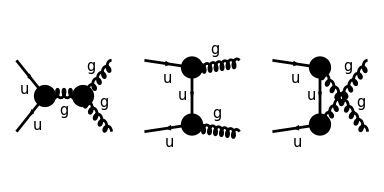

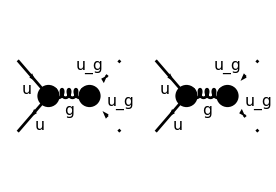

((ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col5^Glu3).(γ·(k_1-p_2)+m_u).(-ⅈ g_s γ^Lor2 T_Col5Col1^Glu4).(φ(p_1,m_u)))/((p_2-k_1)^2-m_u^2)+((ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor2 T_Col2Col5^Glu4).(γ·(k_2-p_2)+m_u).(-ⅈ g_s γ^Lor1 T_Col5Col1^Glu3).(φ(p_1,m_u)))/((p_2-k_2)^2-m_u^2)-1/(k_1+k_2)^2 g_s g^Lor3Lor4 (ε^*)^Lor1(k_1) (ε^*)^Lor2(k_2) f^Glu3Glu4Glu5 ((k_1+2 k_2)^Lor1 g^Lor2Lor4+(-2 k_1-k_2)^Lor2 g^Lor1Lor4+(k_1-k_2)^Lor4 g^Lor1Lor2) (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor3 T_Col2Col1^Glu5).(φ(p_1,m_u))-(g_s k_1^Lor2 g^Lor1Lor2 f^Glu3Glu4Glu5 (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2+(g_s k_2^Lor2 g^Lor1Lor2 f^Glu3Glu4Glu5 (φ(-p_2,m_u)).(-ⅈ g_s γ^Lor1 T_Col2Col1^Glu5).(φ(p_1,m_u)))/(k_1+k_2)^2

```mathematica
Paint[diagsG, ColumnsXRows -> {3, 1}, Numbering -> None,SheetHeader->None,ImageSize->{384,192}];
Paint[Ghosts,ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{276,192}];
QQbar+QQbarGhosts
```

```mathematica
My Calculations compared to FeynCalc Calculation
```

```mathematica
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 1]-Subscript[p, 2],Subscript[m, q]]]
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 2]-Subscript[p, 2],Subscript[m, q]]]
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 1]-Subscript[p, 1],Subscript[m, q]]]
FeynAmpDenominator[PropagatorDenominatorExplicit[Subscript[k, 2]-Subscript[p, 1],Subscript[m, q]]]
FeyncalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 1],D]^2->0}
FeyncalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[p, 2],D]^2->Subscript[p, 2]^2}/.{Momentum[Subscript[k, 2],D]^2->0}
MycalcDenominator1/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 1],D]^2->0}
MycalcDenominator2/.{Subscript[m, q]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[p, 1],D]^2->Subscript[p, 1]^2}/.{Momentum[Subscript[k, 2],D]^2->0}
M1PropFeynCalc
M2PropFeynCalc
M1PropMyCalc
M2PropMyCalc
```

1/((k_1-p_2)^2-m_q^2)

1/((k_2-p_2)^2-m_q^2)

1/((k_1-p_1)^2-m_q^2)

1/((k_2-p_1)^2-m_q^2)

-2 k_1 p_2

-2 k_2 p_2

-2 k_1 p_1

-2 k_2 p_1

-(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2)

-(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2)

-(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1)

-(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1)

```mathematica
M3FCS=1/SMP["g_s"] FrontCoeffFC1*(GAD[μ]*SUNT[c]*(GluonPropagator[Subscript[k, 3],μ,a,σ,c]//Explicit)*(GluonVertex[Subscript[k, 1],μ,a,Subscript[k, 2],ν,b,Subscript[k, 3],σ,c]//Explicit))
M3MCS=1/SMP["g_s"] FrontCoeffMC1*(GAD[μ]*SUNT[c]*(GluonPropagator[Subscript[k, 3],μ,a,σ,c]//Explicit)*(GluonVertex[Subscript[k, 2],μ,a,Subscript[k, 1],ν,b,Subscript[k, 3],σ,c]//Explicit))
M3FCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}//FullSimplify
M3MCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}/.{SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]]->SUNF[a,b,c]}//FullSimplify
M3FCOrder
M3MCOrder
```

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc ((k_2^μ-k_3^μ) g^νσ+(k_3^ν-k_1^ν) g^μσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/k_3^2

-(ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc ((k_1^μ-k_3^μ) g^νσ+(k_3^ν-k_2^ν) g^μσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/k_3^2

-1/(-k_1-k_2)^2 ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc ((k_2^μ-(-k_1-k_2)^μ) g^νσ+((-k_1-k_2)^ν-k_1^ν) g^μσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q))

-1/(-k_1-k_2)^2 ⅈ γ^μ T^c g_s^2 δ^ac g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc ((k_1^μ-(-k_1-k_2)^μ) g^νσ+((-k_1-k_2)^ν-k_2^ν) g^μσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q))

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_1).(ε^*)^ν(k_2).v̄(p_2,m_q).(-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_2).(ε^*)^ν(k_1).v̄(p_2,m_q).(-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2

```mathematica
M1FCGhostk1Order
M2FCGhostk2Order
M1MCGhostk1Order
M2MCGhostk2Order
```

(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2.(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2).(u(p_1,m_q))

(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2.(u(p_1,m_q))

```mathematica
Total Amplitude(Subscript[M, 1]+Subscript[M, 2]+Subscript[M, 3]+Subscript[M, G1]+Subscript[M, G2])
```

```mathematica
MTotalFC
MTotalMC
```

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_1).(ε^*)^ν(k_2).v̄(p_2,m_q).(-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2+(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2.(u(p_1,m_q))+(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2).(u(p_1,m_q))

-(ⅈ.g_s^2.f^abc.T^c g^μσ.γ^μ.(ε^*)^μ(k_2).(ε^*)^ν(k_1).v̄(p_2,m_q).(-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν).(u(p_1,m_q)))/(k_1+k_2)^2+(g_s v̄(p_2,m_q)).(ⅈ.g_s.f^abc T^c.g^μσ.γ^μ.k_2^σ)/(k_1+k_2)^2.(u(p_1,m_q))+(g_s v̄(p_2,m_q)).(-(ⅈ.g_s f^abc T^c.g^μσ.γ^μ.k_1^σ)/(k_1+k_2)^2).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1).(u(p_1,m_q))+(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q)).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1).(u(p_1,m_q))

## Scratch

```mathematica
%//StandardForm
```

(m.GAD[ν]+(FVD[p,σ] GAD[σ]).GAD[ν]) SpinorU[p,m]

```mathematica
(m.GAD[ν]+Distribute[(FVD[p,σ] GAD[σ])*GAD[ν]]) SpinorU[p,m]
```

(m.γ^ν+γ^ν γ^σ p^σ) (u(p,m))

```mathematica
%/.{GAD[ν]GAD[σ]-> AntiC}
```

(u(p,m)) (p^σ (2 g^νσ-γ^ν.γ^σ)+m.γ^ν)

```mathematica
%//StandardForm
```

(m.GAD[ν]+FVD[p,σ] (-GAD[ν].GAD[σ]+2 MTD[ν,σ])) SpinorU[p,m]

```mathematica
(m GAD[ν]+Distribute[FVD[p,σ] (-GAD[ν]GAD[σ]+2 MTD[ν,σ])]). SpinorU[p,m]
```

(2 p^σ g^νσ+m γ^ν-γ^ν γ^σ p^σ).(u(p,m))

```mathematica
%//StandardForm
```

```mathematica
(Factor[m GAD[ν]-FVD[p,σ] GAD[ν] GAD[σ]]+2 FVD[p,σ] MTD[ν,σ]).SpinorU[p,m]
```

(2 p^σ g^νσ+γ^ν (m-γ^σ p^σ)).(u(p,m))

```mathematica
%//StandardForm
```

(GAD[ν] (m-FVD[p,σ] GAD[σ])+2 FVD[p,σ] MTD[ν,σ]).SpinorU[p,m]

```mathematica
(GAD[ν] (m-FVD[p,σ] GAD[σ])+2 FVD[p,σ] MTD[ν,σ])SpinorU[p,m]//Contract1
ChangeDimension[%//Contract//Simplify,D]
%//Contract
%/.{(m-DiracGamma[Momentum[p,D],D]) Spinor[Momentum[p,D],m,1]->0}
```

(u(p,m)) (2 p^σ g^νσ+γ^ν (m-γ^σ p^σ))

(γ^ν (m-γ·p)+2 p^ν) (φ(p,m))

γ^ν (m-γ·p) (φ(p,m))+2 p^ν (φ(p,m))

2 p^ν (φ(p,m))

```mathematica
(Contract[GAD[σ]FVD[p,σ]]+m).GAD[ν]*Spinor[Momentum[p,D],m,1]==%
```

(m+γ·p).γ^ν (φ(p,m))==2 p^ν (φ(p,m))

```mathematica
M3FCS/.{Subscript[k, 3]->-(Subscript[k, 1]+Subscript[k, 2])}//FullSimplify//Contract
```

(ⅈ D T^c g_s^3 δ^ac (ε^*(k_2)·k_1) f^abc γ·ε^*(k_1) (φ((p̄)_1,m_q)) (φ(-(p̄)_2,m_q)))/(-k_1-k_2)^2-(ⅈ D T^c g_s^3 δ^ac (-(ε^*(k_2)·k_1)-ε^*(k_2)·k_2) f^abc γ·ε^*(k_1) (φ((p̄)_1,m_q)) (φ(-(p̄)_2,m_q)))/(-k_1-k_2)^2+(ⅈ T^c g_s^3 δ^ac γ·(-k_1-k_2) (ε^*(k_1)·ε^*(k_2)) f^abc (φ((p̄)_1,m_q)) (φ(-(p̄)_2,m_q)))/(-k_1-k_2)^2-(ⅈ T^c g_s^3 δ^ac γ·k_2 (ε^*(k_1)·ε^*(k_2)) f^abc (φ((p̄)_1,m_q)) (φ(-(p̄)_2,m_q)))/(-k_1-k_2)^2-(ⅈ T^c g_s^3 δ^ac (ε^*(k_2)·k_1) f^abc γ·ε^*(k_1) (φ((p̄)_1,m_q)) (φ(-(p̄)_2,m_q)))/(-k_1-k_2)^2+(ⅈ T^c g_s^3 δ^ac (ε^*(k_2)·k_2) f^abc γ·ε^*(k_1) (φ((p̄)_1,m_q)) (φ(-(p̄)_2,m_q)))/(-k_1-k_2)^2

```mathematica
%//StandardForm
```

ⅈ DiracGamma[Momentum[-k_1-k_2,D],D] FeynAmpDenominator[PropagatorDenominator[Momentum[-k_1-k_2,D],0]] Pair[Momentum[Polarization[k_1,-ⅈ],D],Momentum[Polarization[k_2,-ⅈ],D]] SMP[g_s]^3 Spinor[Momentum[p_1],m_q,1] Spinor[-Momentum[p_2],m_q,1] SUNDelta[SUNIndex[a],SUNIndex[c]] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]-ⅈ DiracGamma[Momentum[k_2,D],D] FeynAmpDenominator[PropagatorDenominator[Momentum[-k_1-k_2,D],0]] Pair[Momentum[Polarization[k_1,-ⅈ],D],Momentum[Polarization[k_2,-ⅈ],D]] SMP[g_s]^3 Spinor[Momentum[p_1],m_q,1] Spinor[-Momentum[p_2],m_q,1] SUNDelta[SUNIndex[a],SUNIndex[c]] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]-ⅈ DiracGamma[Momentum[Polarization[k_1,-ⅈ],D],D] FeynAmpDenominator[PropagatorDenominator[Momentum[-k_1-k_2,D],0]] Pair[Momentum[Polarization[k_2,-ⅈ],D],Momentum[k_1,D]] SMP[g_s]^3 Spinor[Momentum[p_1],m_q,1] Spinor[-Momentum[p_2],m_q,1] SUNDelta[SUNIndex[a],SUNIndex[c]] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]+ⅈ D DiracGamma[Momentum[Polarization[k_1,-ⅈ],D],D] FeynAmpDenominator[PropagatorDenominator[Momentum[-k_1-k_2,D],0]] Pair[Momentum[Polarization[k_2,-ⅈ],D],Momentum[k_1,D]] SMP[g_s]^3 Spinor[Momentum[p_1],m_q,1] Spinor[-Momentum[p_2],m_q,1] SUNDelta[SUNIndex[a],SUNIndex[c]] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]-ⅈ D DiracGamma[Momentum[Polarization[k_1,-ⅈ],D],D] FeynAmpDenominator[PropagatorDenominator[Momentum[-k_1-k_2,D],0]] (-Pair[Momentum[Polarization[k_2,-ⅈ],D],Momentum[k_1,D]]-Pair[Momentum[Polarization[k_2,-ⅈ],D],Momentum[k_2,D]]) SMP[g_s]^3 Spinor[Momentum[p_1],m_q,1] Spinor[-Momentum[p_2],m_q,1] SUNDelta[SUNIndex[a],SUNIndex[c]] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]+ⅈ DiracGamma[Momentum[Polarization[k_1,-ⅈ],D],D] FeynAmpDenominator[PropagatorDenominator[Momentum[-k_1-k_2,D],0]] Pair[Momentum[Polarization[k_2,-ⅈ],D],Momentum[k_2,D]] SMP[g_s]^3 Spinor[Momentum[p_1],m_q,1] Spinor[-Momentum[p_2],m_q,1] SUNDelta[SUNIndex[a],SUNIndex[c]] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[SUNIndex[c]]

```mathematica
M3FC
M3MC
```

-(ⅈ γ^μ T^c g_s^2 g^μσ (ε^*)^μ(k_1) (ε^*)^ν(k_2) f^abc (-1. (2 k_1^ν+k_2^ν) g^μσ+(k_1^μ+2 k_2^μ) g^νσ+(k_1^σ-k_2^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2

-(ⅈ γ^μ T^c g_s^2 g^μσ (ε^*)^μ(k_2) (ε^*)^ν(k_1) f^abc (-1. (k_1^ν+2 k_2^ν) g^μσ+(2 k_1^μ+k_2^μ) g^νσ+(k_2^σ-k_1^σ) g^μν) v̄(p_2,m_q) (u(p_1,m_q)))/(k_1+k_2)^2

```mathematica
%%//StandardForm
%%//StandardForm
```

-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k_1+k_2,D],0]] GAD[μ] Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]] Pair[LorentzIndex[μ,D],Momentum[Polarization[k_1,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[k_2,-ⅈ],D]] (-1. (2 FVD[k_1,ν]+FVD[k_2,ν]) Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]]+(FVD[k_1,μ]+2 FVD[k_2,μ]) Pair[LorentzIndex[ν,D],LorentzIndex[σ,D]]+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] (Pair[LorentzIndex[σ,D],Momentum[k_1,D]]-Pair[LorentzIndex[σ,D],Momentum[k_2,D]])) SMP[g_s]^2 SpinorU[p_1,m_q] SpinorVBar[p_2,m_q] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[c]

-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[k_1+k_2,D],0]] GAD[μ] Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]] Pair[LorentzIndex[μ,D],Momentum[Polarization[k_2,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[k_1,-ⅈ],D]] (-1. (FVD[k_1,ν]+2 FVD[k_2,ν]) Pair[LorentzIndex[μ,D],LorentzIndex[σ,D]]+(2 FVD[k_1,μ]+FVD[k_2,μ]) Pair[LorentzIndex[ν,D],LorentzIndex[σ,D]]+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] (-Pair[LorentzIndex[σ,D],Momentum[k_1,D]]+Pair[LorentzIndex[σ,D],Momentum[k_2,D]])) SMP[g_s]^2 SpinorU[p_1,m_q] SpinorVBar[p_2,m_q] SUNF[SUNIndex[a],SUNIndex[b],SUNIndex[c]] SUNT[c]

```mathematica
M1FC=FrontCoeffFC1.M1PropFeynCalc
M2FC=FrontCoeffFC2.M2PropFeynCalc
M1MC=FrontCoeffMC1.M1PropMyCalc
M2MC=FrontCoeffMC2.M2PropMyCalc
```

(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q) (u(p_1,m_q))).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_2^ν))/(2 k_1 p_2)

(g_s^2 (ε^*)^μ(k_1) (ε^*)^ν(k_2) v̄(p_2,m_q) (u(p_1,m_q))).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_2^μ))/(2 k_2 p_2)

(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q) (u(p_1,m_q))).(T^a.T^b (γ^μ (γ·k_1).γ^ν-2 γ^μ p_1^ν))/(2 k_1 p_1)

(g_s^2 (ε^*)^μ(k_2) (ε^*)^ν(k_1) v̄(p_2,m_q) (u(p_1,m_q))).(T^b.T^a (γ^ν (γ·k_2).γ^μ-2 γ^ν p_1^μ))/(2 k_2 p_1)

```mathematica
(FrontCoeffFC1/(SMP["g_s"]Pair[LorentzIndex[ν,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]])).Distribute[SMP["g_s"](a+b)]
```

(g_s (ε^*)^μ(k_1) v̄(p_2,m_q) (u(p_1,m_q))).(a g_s+b g_s)

```mathematica
(FrontCoeffMC1/(SMP["g_s"]Pair[LorentzIndex[μ,D],Momentum[Polarization[Subscript[k, 2],-ⅈ],D]])).Distribute[SMP["g_s"](M1MCContractk2mu+M2MCContractk2mu+(-M3MCContractk2mu//Cancel//Expand))]
```

(g_s (ε^*)^ν(k_1) v̄(p_2,m_q) (u(p_1,m_q))).((ⅈ γ^ν T^c g_s (k_2·p_1) f^abc)/(k_2 p_1)-(ⅈ T^c g_s p_1^ν γ·k_2 f^abc)/(k_1 p_1)+(ⅈ T^c g_s f^abc (γ·k_2).(γ·k_1).γ^ν)/(2 k_1 p_1)-(ⅈ T^c g_s f^abc γ^ν.(γ·k_2).(γ·k_2))/(2 k_2 p_1)+(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/(2 (k_1·k_2))+(ⅈ T^c g_s k_2^ν γ·k_1 f^abc)/(2 (k_1·k_2))+(ⅈ T^c g_s k_2^ν γ·k_2 f^abc)/(2 (k_1·k_2))-ⅈ γ^ν T^c g_s f^abc-(γ^ν g_s T^a.T^b (k_2·p_1))/(k_2 p_1)+(g_s T^a.T^b γ^ν.(γ·k_2).(γ·k_2))/(2 k_2 p_1)-(g_s p_1^ν T^b.T^a γ·k_2)/(k_1 p_1)+(g_s T^b.T^a (γ·k_2).(γ·k_1).γ^ν)/(2 k_1 p_1))

```mathematica
Distribute[SMP["g_s"](M1MCContractk2mu+M2MCContractk2mu+(-M3MCContractk2mu//Cancel//Expand))]
```

(ⅈ γ^ν T^c g_s (k_2·p_1) f^abc)/(k_2 p_1)-(ⅈ T^c g_s p_1^ν γ·k_2 f^abc)/(k_1 p_1)+(ⅈ T^c g_s f^abc (γ·k_2).(γ·k_1).γ^ν)/(2 k_1 p_1)-(ⅈ T^c g_s f^abc γ^ν.(γ·k_2).(γ·k_2))/(2 k_2 p_1)+(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/(2 (k_1·k_2))+(ⅈ T^c g_s k_2^ν γ·k_1 f^abc)/(2 (k_1·k_2))+(ⅈ T^c g_s k_2^ν γ·k_2 f^abc)/(2 (k_1·k_2))-ⅈ γ^ν T^c g_s f^abc-(γ^ν g_s T^a.T^b (k_2·p_1))/(k_2 p_1)+(g_s T^a.T^b γ^ν.(γ·k_2).(γ·k_2))/(2 k_2 p_1)-(g_s p_1^ν T^b.T^a γ·k_2)/(k_1 p_1)+(g_s T^b.T^a (γ·k_2).(γ·k_1).γ^ν)/(2 k_1 p_1)

```mathematica
Distribute[SMP["g_s"](M1MCContractk2mu+M2MCContractk2mu+(-M3MCContractk2mu//Cancel//Expand))]/.{Momentum[Subscript[p, 1],D]->Momentum[Subscript[k, 1],D]}
```

(ⅈ γ^ν T^c g_s (k_1·k_2) f^abc)/(k_1 k_2)+(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/(2 (k_1·k_2))+(ⅈ T^c g_s k_2^ν γ·k_1 f^abc)/(2 (k_1·k_2))+(ⅈ T^c g_s k_2^ν γ·k_2 f^abc)/(2 (k_1·k_2))-(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/k_1^2-(ⅈ T^c g_s f^abc γ^ν.(γ·k_2).(γ·k_2))/(2 k_1 k_2)+(ⅈ T^c g_s f^abc (γ·k_2).(γ·k_1).γ^ν)/(2 k_1^2)-ⅈ γ^ν T^c g_s f^abc-(γ^ν g_s (k_1·k_2) T^a.T^b)/(k_1 k_2)+(g_s T^a.T^b γ^ν.(γ·k_2).(γ·k_2))/(2 k_1 k_2)-(g_s k_1^ν T^b.T^a γ·k_2)/k_1^2+(g_s T^b.T^a (γ·k_2).(γ·k_1).γ^ν)/(2 k_1^2)

```mathematica
Distribute[SMP["g_s"](M1MCContractk2mu+M2MCContractk2mu+(-M3MCContractk2mu//Cancel//Expand))]/.{Momentum[Subscript[p, 1],D]->Momentum[Subscript[k, 1],D]}/.{Pair[Momentum[Subscript[k, 1],D],Momentum[Subscript[k, 2],D]]->(Momentum[Subscript[k, 1],D] *Momentum[Subscript[k, 2],D])}
```

(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/(2 k_1 k_2)-(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/k_1^2+(ⅈ T^c g_s k_2^ν γ·k_1 f^abc)/(2 k_1 k_2)+(ⅈ T^c g_s k_2^ν γ·k_2 f^abc)/(2 k_1 k_2)-(ⅈ T^c g_s f^abc γ^ν.(γ·k_2).(γ·k_2))/(2 k_1 k_2)+(ⅈ T^c g_s f^abc (γ·k_2).(γ·k_1).γ^ν)/(2 k_1^2)+(g_s T^a.T^b γ^ν.(γ·k_2).(γ·k_2))/(2 k_1 k_2)-(g_s k_1^ν T^b.T^a γ·k_2)/k_1^2+(g_s T^b.T^a (γ·k_2).(γ·k_1).γ^ν)/(2 k_1^2)-γ^ν g_s T^a.T^b

```mathematica
%/.{SUNT[b,a]->-ⅈ SUNF[a,b,c]SUNT[c]}
%/.{SUNT[a,b]->ⅈ SUNF[a,b,c]SUNT[c]}
```

(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/(2 k_1 k_2)+(ⅈ T^c g_s k_2^ν γ·k_1 f^abc)/(2 k_1 k_2)+(ⅈ T^c g_s k_2^ν γ·k_2 f^abc)/(2 k_1 k_2)-(ⅈ T^c g_s f^abc γ^ν.(γ·k_2).(γ·k_2))/(2 k_1 k_2)+(g_s T^a.T^b γ^ν.(γ·k_2).(γ·k_2))/(2 k_1 k_2)-γ^ν g_s T^a.T^b

(ⅈ T^c g_s k_1^ν γ·k_2 f^abc)/(2 k_1 k_2)+(ⅈ T^c g_s k_2^ν γ·k_1 f^abc)/(2 k_1 k_2)+(ⅈ T^c g_s k_2^ν γ·k_2 f^abc)/(2 k_1 k_2)-ⅈ γ^ν T^c g_s f^abc